```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

```mathematica
<<MaTeX`
```

```mathematica
dataHR=Import["/Users/apatron/Desktop/codes/metropolis/numerical diagonalisation/HRbranch.dat"];
dataHC=Import["/Users/apatron/Desktop/codes/metropolis/numerical diagonalisation/HCbranch.dat"];
dataCR=Import["/Users/apatron/Desktop/codes/metropolis/numerical diagonalisation/CRbranch.dat"];

avecHR=dataHR[[All,1]];
avecHC=dataHC[[All,1]];
avecCR=dataCR[[All,1]];

alphavecHR=dataHR[[All,2]];
alphavecHC=dataHC[[All,2]];
alphavecCR=dataCR[[All,2]];

HRbranch = Transpose@{avecHR,alphavecHR};
HCbranch = Transpose@{avecHC,alphavecHC};
CRbranch = Transpose@{avecCR,alphavecCR};

fHR=Interpolation[HRbranch,InterpolationOrder->2];
fHC=Interpolation[HCbranch,InterpolationOrder->2];
fCR=Interpolation[CRbranch,InterpolationOrder->2];
xcoord=2.08;
```

```mathematica
datalambda=Import["/Users/apatron/Desktop/codes/metropolis/numerical diagonalisation/lambda_map.dat"];
dataIPR=Import["/Users/apatron/Desktop/codes/metropolis/numerical diagonalisation/ipr_map.dat"];
dataFidel=Import["/Users/apatron/Desktop/codes/metropolis/numerical diagonalisation/fidel_map.dat"];
```

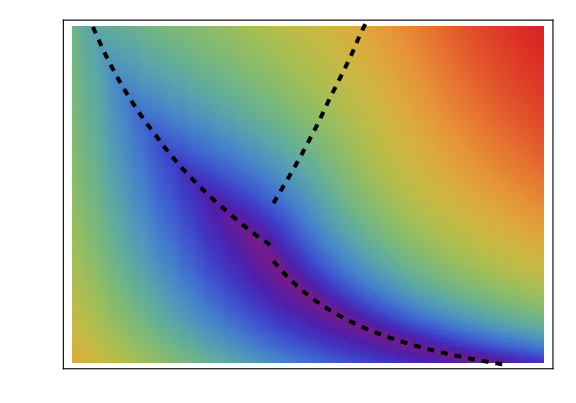

```mathematica
plotlambda=Show[ListDensityPlot[datalambda,ColorFunction->"Rainbow",PlotLegends->BarLegend[{"Rainbow",{0.6,1}},LabelStyle->Directive[FontSize->20,Black],Ticks->Table[{Round[x,10^-2],MaTeX[NumberForm[N[Round[x,10^-2]],{3,1}],Magnification->1.7]},{x,0,1.0,0.1}],LegendMarkerSize->250,LegendLabel->MaTeX["\\Lambda",Magnification->2],LegendMargins->{{-4,0},{35,0}}]],Plot[fHR[x],{x,xcoord,3.29},PlotStyle->{Dashed,Black,Thickness[0.005]}],Plot[fHC[x],{x,1.131,xcoord},PlotStyle->{Dashed,Black,Thickness[0.005]}],Plot[fCR[x],{x,xcoord,2.6},PlotStyle->{Dashed,Black,Thickness[0.005]}],Frame->True,FrameStyle->Directive[Black,28,FontFamily->"Times New Roman"],FrameLabel->MaTeX[{"a","\\alpha"},Magnification->2],FrameTicks->{{Table[{i,MaTeX[i,Magnification->2]},{i,0,4}],None},{Table[{1 + i*0.5,MaTeX[NumberForm[1+0.5*i,{2,1}],Magnification->2]},{i,0,7}],None}},ImageSize->Large,AspectRatio->0.7]
```

```mathematica
Export["/Users/apatron/Desktop/codes/metropolis/numerical diagonalisation/lambda_map_new2.pdf",plotlambda]
```

/Users/apatron/Desktop/codes/metropolis/numerical diagonalisation/lambda_map_new2.pdf

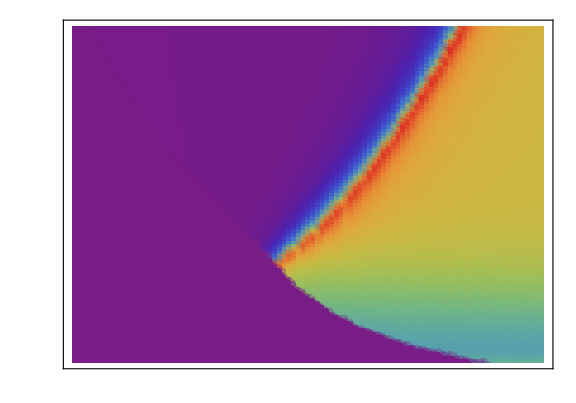

```mathematica
plotIPR=Show[ListDensityPlot[dataIPR,ColorFunction->"Rainbow",PlotLegends->BarLegend[{"Rainbow",{0,1}},LabelStyle->Directive[FontSize->20,Black],Ticks->Table[{Round[x,10^-2],MaTeX[NumberForm[N[Round[x,10^-2]],{3,1}],Magnification->1.7]},{x,0,1.0,0.2}],LegendMarkerSize->250,LegendLabel->MaTeX["\\text{IPR}",Magnification->2],LegendMargins->{{-4,0},{35,0}}]],Frame->True,FrameStyle->Directive[Black,28,FontFamily->"Times New Roman"],FrameLabel->MaTeX[{"a","\\alpha"},Magnification->2],FrameTicks->{{Table[{i,MaTeX[i,Magnification->2]},{i,0,4}],None},{Table[{1 + i*0.5,MaTeX[NumberForm[1+0.5*i,{2,1}],Magnification->2]},{i,0,7}],None}},ImageSize->Large,AspectRatio->0.7]
```

```mathematica
Export["/Users/apatron/Desktop/codes/metropolis/numerical diagonalisation/IPR_map_new.pdf",plotIPR]
```

/Users/apatron/Desktop/codes/metropolis/numerical diagonalisation/IPR_map_new.pdf

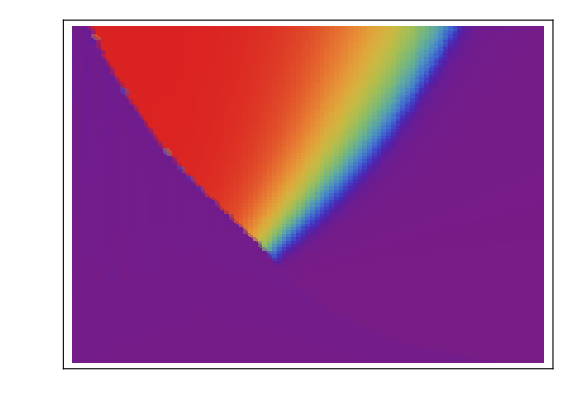

```mathematica
plotFID=Show[ListDensityPlot[dataFidel,ColorFunction->"Rainbow",PlotLegends->BarLegend[{"Rainbow",{0,1}},LabelStyle->Directive[FontSize->20,Black],Ticks->Table[{Round[x,10^-2],MaTeX[NumberForm[N[Round[x,10^-2]],{3,1}],Magnification->2]},{x,0,1.0,0.2}],LegendMarkerSize->250,LegendLabel->MaTeX["\\text{Fid.}",Magnification->2],LegendMargins->{{-4,0},{35,0}}]],Frame->True,FrameStyle->Directive[Black,28,FontFamily->"Times New Roman"],FrameLabel->MaTeX[{"a","\\alpha"},Magnification->2],FrameTicks->{{Table[{i,MaTeX[i,Magnification->2]},{i,0,4}],None},{Table[{1 + i*0.5,MaTeX[NumberForm[1+0.5*i,{2,1}],Magnification->2]},{i,0,7}],None}},ImageSize->Large,AspectRatio->0.7]
```

```mathematica
Export["/Users/apatron/Desktop/codes/metropolis/numerical diagonalisation/Fidel_map_new.pdf",plotFID]
```

/Users/apatron/Desktop/codes/metropolis/numerical diagonalisation/Fidel_map_new.pdf

```mathematica
Min[datalambda[[All,3]]]
```

0.617007